```mathematica
ggenb[z_]:=1+(z Conjugate[z])^Δσ+(z Conjugate[z]/((1-z )Conjugate[1-z]))^Δσ
```

```mathematica
g[h_,hb_,z_]:=1/(KroneckerDelta[h,hb]+1)(z^h Conjugate[z]^hb Hypergeometric2F1[h,h,2h,z]Hypergeometric2F1[hb,hb,2hb,Conjugate[z]]+Conjugate[z]^h z^hb Hypergeometric2F1[h,h,2h,Conjugate[z]]Hypergeometric2F1[hb,hb,2hb,z])
```

```mathematica
crossingEq[n_]:=Sum[C[i](Abs[z-1]^(2 Δσ)g[h[i],hb[i],z]-Abs[z]^(2Δσ)g[h[i],hb[i],1-z]),{i,1,n}]+Abs[z-1]^(2 Δσ)-Abs[z]^(2 Δσ)/.{h[i_]->(Δ[i]+s[i])/2,hb[i_]->(Δ[i]-s[i])/2}
```

```mathematica
allZpts=Table[{z->1/2+RandomVariate[NormalDistribution[0,1/5],WorkingPrecision->50]
Exp[I*(Pi-Pi/2*RandomReal[WorkingPrecision->50])]},1000];
```

```mathematica
leastSqRew1[deltas_,spins_,dσ_,nrand_,nstat_]:=Module[{cs,G,v,c,r,allZpts,means,stds},
cs=Table[
allZpts=Table[{z->1/2+RandomVariate[NormalDistribution[0,1/5],WorkingPrecision->50]
Exp[I*(Pi-Pi/2*RandomReal[WorkingPrecision->50])]},nrand];
v=crossingEq[4]/.s[i_]->spins[[i]]/.Δ[i_]->deltas[[i]]/.Δσ->dσ/.allZpts/.C[i_]->0//Chop;
G=D[crossingEq[4],{Array[C,4],1}]/.s[i_]->spins[[i]]/.Δ[i_]->deltas[[i]]/.Δσ->dσ/.allZpts//Chop;
c=(Inverse[(Transpose[G].G)].Transpose[G]).v;
c,{nstat}];
means=Mean[cs];
stds=StandardDeviation[cs];
r=-Log[Abs[stds/means][[;;2]]//Total];
{cs,r}]
```

```mathematica
leastSqRew1[deltasYL+{0,0,0,-1},spinsYL,-4/10,10,20]
```

Part::pkspec1: The expression i$ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

```mathematica
{,3.2586894617475999306589697039653940144390732073097894390304`40.29861360930143}
```

```mathematica
leastSqRew1[deltasYL,spinsYL,-4/10,10,20][[-1]]
```

Part::pkspec1: The expression i$ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

4.157389702993588539010460268180455435266

```mathematica
deltasYL+{0,0,0,1}
```

{-2/5,2,18/5,43/5}

```mathematica
Abs[crossingEq[4]/.Δσ->-4/10/.Δ[i_]->{-2/5,2,18/5,43/5}[[i]]/.s[i_]->spinsYL[[i]]/.C[i_]->%609[[1]][[i]]/.z->x+I*y//Evaluate]
```

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Abs[1/Abs[-1+x+ⅈ y]^(4/5)-1/Abs[x+ⅈ y]^(4/5)+3.65926498599953392925763040460147200219 ((Hypergeometric2F1[-1/5,-1/5,-2/5,x+ⅈ y] Hypergeometric2F1[-1/5,-1/5,-2/5,Conjugate[x]-ⅈ Conjugate[y]])/((x+ⅈ y)^(1/5) Abs[-1+x+ⅈ y]^(4/5) (Conjugate[x]-ⅈ Conjugate[y])^(1/5))-(Hypergeometric2F1[-1/5,-1/5,-2/5,1-x-ⅈ y] Hypergeometric2F1[-1/5,-1/5,-2/5,1-Conjugate[x]+ⅈ Conjugate[y]])/((1-x-ⅈ y)^(1/5) Abs[x+ⅈ y]^(4/5) (1-Conjugate[x]+ⅈ Conjugate[y])^(1/5)))+0.0006736879355303551570398276538721732142 (1/Abs[-1+x+ⅈ y]^(4/5)(((x+ⅈ y)^(19/5) Hypergeometric2F1[-1/5,-1/5,-2/5,Conjugate[x]-ⅈ Conjugate[y]] Hypergeometric2F1[19/5,19/5,38/5,x+ⅈ y])/(Conjugate[x]-ⅈ Conjugate[y])^(1/5)+1/(x+ⅈ y)^(1/5)(Conjugate[x]-ⅈ Conjugate[y])^(19/5) Hypergeometric2F1[-1/5,-1/5,-2/5,x+ⅈ y] Hypergeometric2F1[19/5,19/5,38/5,Conjugate[x]-ⅈ Conjugate[y]])-1/Abs[x+ⅈ y]^(4/5)(((1-x-ⅈ y)^(19/5) Hypergeometric2F1[-1/5,-1/5,-2/5,1-Conjugate[x]+ⅈ Conjugate[y]] Hypergeometric2F1[19/5,19/5,38/5,1-x-ⅈ y])/(1-Conjugate[x]+ⅈ Conjugate[y])^(1/5)+1/(1-x-ⅈ y)^(1/5)(1-Conjugate[x]+ⅈ Conjugate[y])^(19/5) Hypergeometric2F1[-1/5,-1/5,-2/5,1-x-ⅈ y] Hypergeometric2F1[19/5,19/5,38/5,1-Conjugate[x]+ⅈ Conjugate[y]]))-0.000104974766254768649454505239305719657 (1/Abs[-1+x+ⅈ y]^(4/5)(x+ⅈ y)^(43/10) (Conjugate[x]-ⅈ Conjugate[y])^(43/10) Hypergeometric2F1[43/10,43/10,43/5,x+ⅈ y] Hypergeometric2F1[43/10,43/10,43/5,Conjugate[x]-ⅈ Conjugate[y]]-1/Abs[x+ⅈ y]^(4/5)(1-x-ⅈ y)^(43/10) (1-Conjugate[x]+ⅈ Conjugate[y])^(43/10) Hypergeometric2F1[43/10,43/10,43/5,1-x-ⅈ y] Hypergeometric2F1[43/10,43/10,43/5,1-Conjugate[x]+ⅈ Conjugate[y]])+0.017553632374387152776835851029909969181 (-1/Abs[x+ⅈ y]^(4/5)((6 (1-x-ⅈ y)^2 (2-2 (x+ⅈ y)+Log[x+ⅈ y]+(x+ⅈ y) Log[x+ⅈ y]))/(-1+x+ⅈ y)^3+(6 (1-Conjugate[x]+ⅈ Conjugate[y])^2 (2-2 (Conjugate[x]-ⅈ Conjugate[y])+Log[Conjugate[x]-ⅈ Conjugate[y]]+(Conjugate[x]-ⅈ Conjugate[y]) Log[Conjugate[x]-ⅈ Conjugate[y]]))/(-1+Conjugate[x]-ⅈ Conjugate[y])^3)+1/Abs[-1+x+ⅈ y]^(4/5)((6 (-2 (x+ⅈ y)-2 Log[1-x-ⅈ y]+(x+ⅈ y) Log[1-x-ⅈ y]))/(x+ⅈ y)+(6 (-2 (Conjugate[x]-ⅈ Conjugate[y])-2 Log[1-Conjugate[x]+ⅈ Conjugate[y]]+(Conjugate[x]-ⅈ Conjugate[y]) Log[1-Conjugate[x]+ⅈ Conjugate[y]]))/(Conjugate[x]-ⅈ Conjugate[y])))]

```mathematica
Plot3D[%,{x,0,1/2},{y,0,1/2}]
```

-Graphics3D-

```mathematica
Plot3D[%622/%620,{x,0,1/2},{y,0,1/2}]
```

-Graphics3D-

```mathematica
Abs[crossingEq[4]/.Δσ->-4/10/.Δ[i_]->deltasYL[[i]]/.s[i_]->spinsYL[[i]]/.C[i_]->%610[[1]][[i]]/.z->x+I*y//Evaluate];
```

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

```mathematica
leastSqRew1[deltasYL,spinsYL,-4/10,10,20]
```

Part::pkspec1: The expression i$ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{{3.655773238170570877334503377371974481,0.0178247703145971323082758550398921771,0.00060868030210712772139029809481117209,-0.00014666479374342335564472030300632556},3.3549105217129607476243251610872374}

```mathematica
leastSqRew[deltas_,spins_,dσ_]:=Module[{G,v,c,r},
v=crossingEq[4]/.s[i_]->spins[[i]]/.Δ[i_]->deltas[[i]]/.Δσ->dσ/.allZpts/.C[i_]->0//Chop;
G=D[crossingEq[4],{Array[C,4],1}]/.s[i_]->spins[[i]]/.Δ[i_]->deltas[[i]]/.Δσ->dσ/.allZpts//Chop;
c=(Inverse[(Transpose[G].G)].Transpose[G]).v;
r=-Log[Norm[(G.Inverse[(Transpose[G].G)].Transpose[G]-IdentityMatrix[Length[v]]).v/v]];
{c,r}]
```

```mathematica
leastSqRew[deltasYL,spinsYL,-4/10]
```

```mathematica
leastSqRew[{-2/5,221/110,381/110,38/5},spinsYL,-4/10]
```

Part::pkspec1: The expression i$ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{{3.65620512457996189755787294328234122487,0.017790523787638366634154146820761570328,0.0006091195659978687414172157584761250301,-0.0001495396801288339982262000792681977789},13.65464334738971335434321201132}

```mathematica
leastSqRew[deltasYL,spinsYL,-4/10]
```

Part::pkspec1: The expression i$ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{{3.65461782257193612964025188128595746916,0.017912374424690982660393990839035119537,0.0005884693240168644234329907109929365782,-0.0001634040896700450648324857794384314693},14.10875918302970617012746194367}

```mathematica
spinsIsing={0,2,0,4,6};
```

```mathematica
deltasIsing={1,2,4,4,6};
```

```mathematica
spinsYL={0,2,4,0};
```

```mathematica
deltasYL={-4/10,2,36/10,76/10};
```

```mathematica
(*Parameters for the Gaussian distribution*)mean=1/2; (*Center in the complex plane*)
stdDev=0.1; (*Standard deviation for both real and imaginary parts*)

(*Generate random complex points*)
numPoints=100; (*Number of random points to generate*)
allZpts=Table[{z->RandomVariate[NormalDistribution[Re[mean],stdDev]]+I RandomVariate[NormalDistribution[Im[mean],stdDev]]},{numPoints}];
```

```mathematica
Δσ->-4/10
```

```mathematica
leastSqRew[deltas_,spins_,dσ_]:=Module[{G,v,c,r},
v=crossingEq[4]/.s[i_]->spins[[i]]/.Δ[i_]->deltas[[i]]/.Δσ->dσ/.allZpts/.C[i_]->0//Chop;
G=D[crossingEq[4],{Array[C,4],1}]/.s[i_]->spins[[i]]/.Δ[i_]->deltas[[i]]/.Δσ->dσ/.allZpts//Chop;
c=(Inverse[(Transpose[G].G)].Transpose[G]).v;
r=-Log[Norm[(G.Inverse[(Transpose[G].G)].Transpose[G]-IdentityMatrix[Length[v]]).v/v]];
{c,r}]
```

```mathematica
deltasYL
```

```mathematica
leastSqRew[{-2/5,2.0090909090909093,3.2818181818181817,38/5},spinsYL,-4/10]
```

Part::pkspec1: The expression i$ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{{3.66071,0.0173909,0.000748157,-2.48528×10^-6},7.65542}

```mathematica
deltasYL//N
```

{-0.4,2.,3.6,7.6}

```mathematica
leastSqRew[deltasYL,spinsYL,-4/10]
```

Part::pkspec1: The expression i$ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{{3.65986,0.0174828,0.000693275,-0.000049684},7.70217}

```mathematica
spinsYL
```

{0,2,4,0}

```mathematica
spinsIsing
```

{0,2,0,4,6}

```mathematica
leastSqRew[deltasYL,spinsYL,-4/10]
```

Part::pkspec1: The expression i$ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{{3.65696,0.0177107,0.000637115,-0.0000837862},7.36425}

```mathematica
ParallelTable[{d3,leastSqRew1[{-2/5,2,d3,38/5},spinsYL,-4/10,10,20][[-1]]},{d3,28/10,48/10,1/11}];
```

Part::pkspec1: The expression i$ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::pkspec1: The expression i$ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

```mathematica
ParallelTable[{d2,d3,leastSqRew[{-2/5,d2,d3,38/5},spinsYL,-4/10]},{d2,11/10,28/10,1/11},{d3,28/10,58/10,1/11}];
```

```mathematica
ParallelTable[{d2,d3,leastSqRew[{1,d2,d3,4,6},spinsIsing,1/8]},{d2,11/10,28/10,1/11},{d3,31/10,48/10,1/11}];
```

Part::pkspec1: The expression i$ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::pkspec1: The expression i$ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::pkspec1: The expression i$ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::pkspec1: The expression i$ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::pkspec1: The expression i$ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::pkspec1: The expression i$ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::pkspec1: The expression i$ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

```mathematica
ParallelTable[{d2,d3,leastSqRew[{-2/5,d2,d3,38/5},spinsYL,-4/10]},{d2,11/10,28/10,1/11},{d3,31/10,48/10,1/11}];
```

```mathematica
leastSqRew[{-2/5,2,3.6,38/5},spinsYL,-4/10]
```

Part::pkspec1: The expression i$ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{{3.66036,0.0174715,0.000695596,-0.0000848476},9.14446}

```mathematica
38/5//N
```

7.6

```mathematica
leastSqRew[{-2/5,2,36/10,76/10},spinsYL,-4/10]
```

Part::pkspec1: The expression i$ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{{3.66036359601172417490817047913357474463213,0.017471464349780376136771246944746539667074,0.0006955959881036404278226817457309600453049,-0.0000848476496332621411258603566096427673579},9.144462326281547868963974505758031}

```mathematica
leastSqRew[{-2/5,2,36/10,7},spinsYL,-4/10]
```

Part::pkspec1: The expression i$ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{{3.65928453453263789089288483946027437331737,0.017558767751760534850576555136392410912572,0.0006741705609320936722062388428971635583066,-0.000100776636029874749302447601471151818929},9.284848887122228178941892172150532}

```mathematica
%606
```

```mathematica
ParallelTable[{d4,leastSqRew[{-2/5,2,36/10,d4},spinsYL,-4/10][[-1]]},{d4,7,8,1/11}];
```

Part::pkspec1: The expression i$ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::pkspec1: The expression i$ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::pkspec1: The expression i$ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::pkspec1: The expression i$ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::pkspec1: The expression i$ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

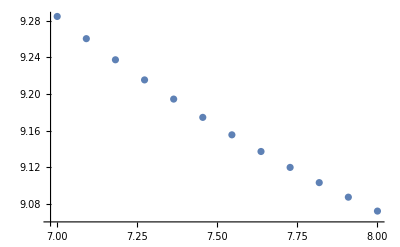

```mathematica
ListPlot[%]
```

```mathematica
ParallelTable[{d3,leastSqRew[{-2/5,2,d3,38/5},spinsYL,-4/10][[-1]]},{d3,31/10,48/10,1/11}];
```

Part::pkspec1: The expression i$ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::pkspec1: The expression i$ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::pkspec1: The expression i$ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::pkspec1: The expression i$ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::pkspec1: The expression i$ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::pkspec1: The expression i$ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::pkspec1: The expression i$ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::pkspec1: The expression i$ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::pkspec1: The expression i$ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::pkspec1: The expression i$ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::pkspec1: The expression i$ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::pkspec1: The expression i$ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::pkspec1: The expression i$ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

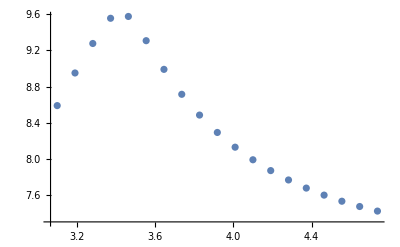

```mathematica
ListPlot[%597]
```

```mathematica
Table[{x[[;;2]],x[[3]][[-1]]}//Flatten,{x,Flatten[%,1]}];
```

```mathematica
ListPlot3D[%]
```

-Graphics3D-

```mathematica
deltasYL
```

{-2/5,2,18/5,38/5}

```mathematica
Flatten[%377,1][[;;,]]
```

```mathematica
{x[[;;2]],x[[3]][[-1]]}//Flatten
```

{11/10,31/10,9.13338}

```mathematica
Table[{x[[;;2]],x[[3]][[-1]]}//Flatten,{x,Flatten[%,1]}];
```

```mathematica
%423[[275]]//N
```

{1.82727,2.98182,7.92018}

```mathematica
Position[%423[[;;,-1]],%423[[;;,-1]]//Max]
```

{{275}}

```mathematica
Position[%571[[;;,3]],Max[%571[[;;,3]]]]
```

{{197}}

```mathematica
%571[[Position[%571[[;;,3]],Max[%571[[;;,3]]]][[1,1]]]]
```

{221/110,401/110,13.867721927457438249547522930401}

```mathematica
%532[[195]]
```

{221/110,381/110,13.9404}

```mathematica
ListPlot3D[%]
```

-Graphics3D-

```mathematica
ListPlot3D[%]
```

-Graphics3D-

```mathematica
ListPlot3D[%383]
```

-Graphics3D-

```mathematica
leastSqRew[{1,2,6,4,6},spinsIsing,1/8]
```

Part::pkspec1: The expression i$ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{{-0.250757,-0.0154089,-0.000115705,-0.000286624},11.7004}

```mathematica
leastSqRew[{1,2,4,4,6},spinsIsing,1/8]
```

Part::pkspec1: The expression i$ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{{-0.250542,-0.0153796,-0.000260388,-0.000296331},12.5647}

```mathematica
leastSqRew[deltasYL,spinsYL,-4/10]
```

Part::pkspec1: The expression i$ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{{3.65696,0.0177107,0.000637115,-0.0000837862},-8.53338}

```mathematica
largeVec=crossingEq[4]/.s[i_]->spinsIsing[[i]]/.Δ[i_]->deltasIsing[[i]]/.Δσ->1/8/.allZpts/.C[i_]->0//Chop;
```

Part::pkspec1: The expression i cannot be used as a part specification.

```mathematica
largeMat=D[crossingEq[4],{Array[C,4],1}]/.s[i_]->spinsIsing[[i]]/.Δ[i_]->deltasIsing[[i]]/.Δσ->1/8/.allZpts//Chop;
```

Part::pkspec1: The expression i cannot be used as a part specification.

```mathematica
largeVec=crossingEq[4]/.s[i_]->spinsYL[[i]]/.Δ[i_]->deltasYL[[i]]/.Δσ->-4/10/.allZpts/.C[i_]->0//Chop;
```

Part::pkspec1: The expression i cannot be used as a part specification.

```mathematica
largeMat=D[crossingEq[4],{Array[C,4],1}]/.s[i_]->spinsYL[[i]]/.Δ[i_]->deltasYL[[i]]/.Δσ->-4/10/.allZpts//Chop;
```

Part::pkspec1: The expression i cannot be used as a part specification.

```mathematica
largeMat=largeMat//Transpose;
```

```mathematica
largeMat0Mean=largeMat-ConstantArray[Mean[largeMat],5]
```

```mathematica
PrincipalComponents[largeMat0Mean]//Dimensions
```

{4,1000}

```mathematica
{U,S,V}=SingularValueDecomposition[largeMat];
```

```mathematica
U.S.Transpose[V].C==largeVec
```

```mathematica
largeMat
```

```mathematica
PrincipalComponents[largeMat//Transpose]//Dimensions
```

{1000,5}

```mathematica
%106[[;;,1]].%106[[;;,2]]
```

6.86496×10^-15

```mathematica
Transpose[%106].%106//Chop
```

{{162.121,0,0,0,0},{0,3.25699,0,0,0},{0,0,0.0257817,0,0},{0,0,0,0.00201643,0},{0,0,0,0,6.97821×10^-9}}

```mathematica
PrincipalComponents[largeMat//Transpose]
```

```mathematica
n=4;
```

```mathematica
n=5; (*for example,choose 3 dimensions*)
Vn=V[[All,1;;n]];       (*N x n matrix of top principal directions*)
A=Transpose[Vn];           (*n x N matrix that projects data into n-dim space*)
```

```mathematica
As=Table[V[[All,1+j*n;;n+j*n]]//Transpose,{j,0,10}]
```

```mathematica
%209//Dimensions
```

{11,4,1000}

```mathematica
Transpose[largeMat]//Dimensions
```

{1000,4}

```mathematica
A//Dimensions
```

{4,4}

```mathematica
A.Transpose[largeMat]
```

{{4.43131,13.0857,7.11031,12.8861,9.29328},{0.453444,1.07843,0.609613,-0.148256,-1.67374},{0.0339636,0.0899721,0.250372,0.114742,0.124766},{0.0249735,0.0546259,0.0305221,-0.00238172,0.0473687}}

```mathematica
A//Dimensions
```

{4,1000}

```mathematica
largeMat//Dimensions
```

{4,1000}

```mathematica
Clear[A]
```

```mathematica
S//Dimensions
```

{4,1000}

```mathematica
S[[4,5]]
```

0.

```mathematica
Diagonal[S]
```

{7.46097,0.877641,0.159012,0.}

```mathematica
Inverse[%209[[2]].Transpose[largeMat]].%209[[2]].largeVec
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{-0.0000239874,-0.0000239874,-0.0000239874,-0.0000239874},{8.51789×10^-6,8.51789×10^-6,8.51789×10^-6,8.51789×10^-6},{«1»},{-0.000171971,-0.000171971,-0.000171971,-0.000171971}} may contain significant numerical errors.

{-2.46554×10^6,-1.54187×10^7,3.22321×10^7,-1.43478×10^7}

```mathematica
largeMat//Dimensions
```

{5,1000}

```mathematica
As//Dimensions
```

{11,5,1000}

```mathematica
largeMat.Inverse[(Transpose[largeMat].largeMat)].Transpose[largeMat]
```

```mathematica
Length[largeVec]
```

1000

```mathematica
(Inverse[(Transpose[largeMat].largeMat)].Transpose[largeMat]).largeVec
```

{-0.250542,-0.0153796,-0.000260388,-0.000296331}

```mathematica
csIsing={0.25,0.015625,0.000219727,0.000244141}
```

{0.25,0.015625,0.000219727,0.000244141}

```mathematica
(Inverse[(Transpose[largeMat].largeMat)].Transpose[largeMat]).largeVec
```

{-0.250633,-0.0153463,-0.000256512,-0.000300971}

```mathematica
Norm[(largeMat.Inverse[(Transpose[largeMat].largeMat)].Transpose[largeMat]-IdentityMatrix[Length[largeVec]]).largeVec]
```

9.01103×10^-6

```mathematica
Table[Inverse[A.Transpose[largeMat]].A.largeVec,{A,As}]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{-0.0016348,-0.0016348,-0.0016348,-0.0016348},{-0.000680806,-0.000680806,-0.000680806,-0.000680806},{-0.00282295,«2»,-«22»},{-0.000585254,-0.000585254,-0.000585254,-0.000585254}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{-0.000121548,-0.000121548,-0.000121548,-0.000121548},{-0.000946295,-0.000946295,-0.000946295,-0.000946295},{«1»},{-0.000697357,-0.000697357,-0.000697357,-0.000697357}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{-0.000317429,-0.000317429,-0.000317429,-0.000317429},{-0.00172231,-0.00172231,-0.00172231,-0.00172231},{«1»},{-0.000403005,-0.000403005,-0.000403005,-0.000403005}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

{{3.65785,0.017646,0.00065232,-0.0000789623},{8.46735×10^11,-8.36058×10^10,-9.15517×10^10,-6.71577×10^11},{-1.20677×10^10,2.00665×10^9,-1.34249×10^9,1.14036×10^10},{-7.47102×10^9,-1.09284×10^10,1.1767×10^10,6.63242×10^9},{8.45846×10^9,-3.18568×10^9,8.43614×10^9,-1.37089×10^10},{7.17014×10^8,-1.82559×10^9,2.99215×10^9,-1.88357×10^9},{7.47617×10^9,-2.98602×10^10,-4.41232×10^9,2.67964×10^10},{1.95191×10^10,-1.86057×10^9,-2.84409×10^9,-1.48144×10^10},{-1.09032×10^10,-3.6257×10^8,7.96117×10^9,3.30462×10^9},{2.30951×10^10,4.5785×10^9,-1.18794×10^8,-2.75548×10^10},{1.07223×10^10,-2.58898×10^9,-8.06269×10^9,-7.06535×10^7}}

```mathematica
A.largeMat
```

Dot::dotsh: Tensors {{-0.0121728,-0.0303808,-0.0111303,-0.0407974,-0.0317986,-0.0207266,-0.0321896,-0.0167473,-0.00541395,-0.0161648,«990»},{«1»},{«1»},{«1»},{0.0200549,-0.00241376,«7»,0.0132897,«990»}} and {{-0.056095,-0.13221,-0.0496451,-0.195285,-0.137505,-0.0912457,-0.164786,-0.0968216,-0.0270861,-0.0891656,«990»},«3»,{-0.105983,-0.295278,«7»,-0.0815702,«990»}} have incompatible shapes.

```mathematica
PrincipalComponents[largeMat]//MatrixRank
```

4

```mathematica
U.S.Transpose[V]
```

```mathematica
U.S.Transpose[V]
```

```mathematica
U.S.Transpose[V]-largeMat0Mean
```

```mathematica
data=largeMat(*your data matrix*);

(*1. Compute the mean of each variable (column mean)*)
colMean=Mean[data];

(*2. Center the data by subtracting the column means from each row*)
centeredData=data-ConstantArray[1,{Dimensions[data][[1]],1}].{colMean};

(*3. Perform SVD on the centered data*)
{U,S,V}=SingularValueDecomposition[centeredData];

(*U:M x M,S:diagonal M x N,V:N x N Columns of V correspond to principal directions (principal components).The singular values in S correspond to the variance explained by each component.PCA Directions=columns of V PCA Scores (coordinates of data in principal component space)=U*S*)

(*The principal component scores (projection of the original data onto the PCs) can be obtained as:*)
scores=centeredData.V;

(*scores is now M x N.Each column of scores corresponds to a principal component,and each row gives the coordinates of an observation in PC space.If you only need the top n principal components,take the first n columns of V and scores.*)

n=2; (*for example,keep the first 2 principal components*)
reducedV=V[[All,1;;n]];      (*N x n matrix of top n principal directions*)
reducedScores=scores[[All,1;;n]]; (*M x n data in PC space*)
```